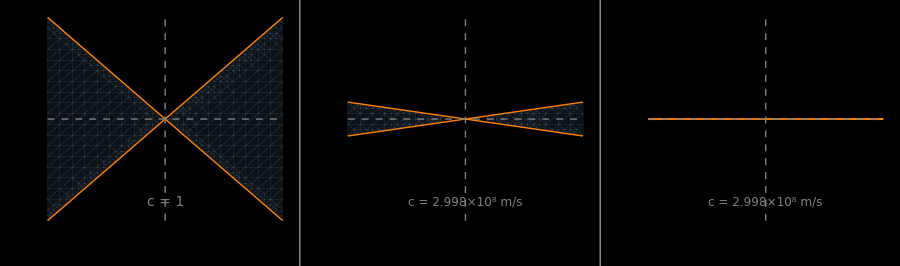

```mathematica
(*Three-panel comparison:light cones with t vertical,x horizontal,square aspect,clean labels*)Clear[makePanel];
makePanel[cVal_,xRange_,tRange_,xLabel_,tLabel_,tag_]:=Module[{yLabelPosition={-.14,.5}},Show[{RegionPlot[Abs[x]>=cVal*Abs[t],{x,-xRange,xRange},{t,-tRange,tRange},PlotRangeClipping->None,PlotStyle->Directive[Opacity[0.18],RGBColor[0.3,0.4,0.5]],BoundaryStyle->None],Plot[Evaluate[{x/cVal,-x/cVal}],{x,-xRange,xRange},PlotStyle->{{Orange,Thick},{Orange,Thick}},Axes->False,PlotRange->{{-xRange,xRange},{-tRange,tRange}}],Graphics[{Gray,Dashed,Line[{{-xRange,0},{xRange,0}}],Line[{{0,-tRange},{0,tRange}}]}],Graphics[Text[Style[tag,12,Gray],{0,-0.82 tRange}]]},Frame->True,FrameLabel->{Style[xLabel,11,White],None},FrameTicksStyle->White,PlotRange->{{-xRange,xRange},{-tRange,tRange}},Background->Black,AxesStyle->White,BaseStyle->{White,11},ImageSize->500,AspectRatio->1,
ImagePadding->{{50,20},{Automatic,Automatic}},
Epilog->{Inset[tLabel,Scaled[yLabelPosition](*position*),{0,0}(*anchor*),Automatic(*scaling for graphics,not text*),{0,1}(*axes orientation*)]}]];

cmPers=Quantity["speed of light"]//UnitConvert//QuantityMagnitude//N;
ckmPers = cmPers/1000;
ckmPerms=ckmPers/1000;

panel1=makePanel[1,1,1,"x (light-sec)","t (sec)",Style["c = 1",14]];

cLabel=Style["c = 3×10^5 km/s",14];
cLabel=StringForm["c = `` m/s",ScientificForm[cmPers,4]];

panel2=makePanel[ckmPerms,1000,20,"x (km)","t (ms)",cLabel];
panel3=makePanel[ckmPers,1000,1,"x (km)","t (s)",cLabel];
elsewhereCaption=Style[
"The classical notion of a global now transforms to 'elsewhere' in special relativity, the grey regions.
While elsewhere doesn't look much like a now when we use units in which c=1,
if we use the more pedestrian mks units it flattens out into a much more now like form.",
TextAlignment->Center,22,FontFamily->"Cambridge"];
GraphicsRow[{panel1,panel2,panel3},Spacings->0.8,Background->Black,ImageMargins->0,ImageSize->900] // Labeled[#,elsewhereCaption,Background->Black,Frame->False]&
```

## Fonts

```mathematica
{#,Style["The quick red fox jumped over the lazy brown dog.",FontFamily->#,20]}&/@$FontFamilies//TableForm
```

3270 Nerd Font | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Cond | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Mono | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Mono Cond | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Mono SemCond | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Propo | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Propo Cond | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font Propo SemCond | The quick red fox jumped over the lazy brown dog.
3270 Nerd Font SemCond | The quick red fox jumped over the lazy brown dog.
aakar | The quick red fox jumped over the lazy brown dog.
Accanthis ADF Std | The quick red fox jumped over the lazy brown dog.
Accanthis ADF Std No2 | The quick red fox jumped over the lazy brown dog.
Accanthis ADF Std No3 | The quick red fox jumped over the lazy brown dog.
Alegreya SC | The quick red fox jumped over the lazy brown dog.
all-the-icons | The quick red fox jumped over the lazy brown dog.
Andika | The quick red fox jumped over the lazy brown dog.
Ani | The quick red fox jumped over the lazy brown dog.
AnjaliOldLipi | The quick red fox jumped over the lazy brown dog.
Annapurna SIL | The quick red fox jumped over the lazy brown dog.
Arimo | The quick red fox jumped over the lazy brown dog.
AR PL UKai CN | The quick red fox jumped over the lazy brown dog.
AR PL UKai HK | The quick red fox jumped over the lazy brown dog.
AR PL UKai TW | The quick red fox jumped over the lazy brown dog.
AR PL UKai TW MBE | The quick red fox jumped over the lazy brown dog.
AR PL UMing CN | The quick red fox jumped over the lazy brown dog.
AR PL UMing HK | The quick red fox jumped over the lazy brown dog.
AR PL UMing TW | The quick red fox jumped over the lazy brown dog.
AR PL UMing TW MBE | The quick red fox jumped over the lazy brown dog.
Asana Math | The quick red fox jumped over the lazy brown dog.
Berenis ADF Pro | The quick red fox jumped over the lazy brown dog.
Berenis ADF Pro Math | The quick red fox jumped over the lazy brown dog.
Bitstream Charter | The quick red fox jumped over the lazy brown dog.
Bitstream Vera Sans | The quick red fox jumped over the lazy brown dog.
Bitstream Vera Sans Mono | The quick red fox jumped over the lazy brown dog.
Bitstream Vera Serif | The quick red fox jumped over the lazy brown dog.
C059 [UKWN] | The quick red fox jumped over the lazy brown dog.
C059 [urw] | The quick red fox jumped over the lazy brown dog.
Cabin | The quick red fox jumped over the lazy brown dog.
Caladea | The quick red fox jumped over the lazy brown dog.
Cantarell | The quick red fox jumped over the lazy brown dog.
Cantarell Extra Bold | The quick red fox jumped over the lazy brown dog.
Cantarell Light | The quick red fox jumped over the lazy brown dog.
Cantarell Thin | The quick red fox jumped over the lazy brown dog.
Carlito | The quick red fox jumped over the lazy brown dog.
Chandas | The quick red fox jumped over the lazy brown dog.
Charis SIL | The quick red fox jumped over the lazy brown dog.
Chilanka | The quick red fox jumped over the lazy brown dog.
Clear Sans | The quick red fox jumped over the lazy brown dog.
Clear Sans Light | The quick red fox jumped over the lazy brown dog.
Clear Sans Medium | The quick red fox jumped over the lazy brown dog.
Clear Sans Thin | The quick red fox jumped over the lazy brown dog.
cmex10 | The quick red fox jumped over the lazy brown dog.
cmmi10 | The quick red fox jumped over the lazy brown dog.
cmr10 | The quick red fox jumped over the lazy brown dog.
cmsy10 | The quick red fox jumped over the lazy brown dog.
Comfortaa | The quick red fox jumped over the lazy brown dog.
Comfortaa Light | The quick red fox jumped over the lazy brown dog.
Comic Neue | The quick red fox jumped over the lazy brown dog.
Comic Neue Light | The quick red fox jumped over the lazy brown dog.
Courier | The quick red fox jumped over the lazy brown dog.
Courier 10 Pitch | The quick red fox jumped over the lazy brown dog.
Cousine | The quick red fox jumped over the lazy brown dog.
D050000L [urw] | The quick red fox jumped over the lazy brown dog.
D050000L [URW ] | The quick red fox jumped over the lazy brown dog.
DejaVu Math TeX Gyre | The quick red fox jumped over the lazy brown dog.
DejaVu Sans | The quick red fox jumped over the lazy brown dog.
DejaVu Sans Condensed | The quick red fox jumped over the lazy brown dog.
DejaVu Sans Mono | The quick red fox jumped over the lazy brown dog.
DejaVu Serif | The quick red fox jumped over the lazy brown dog.
DejaVu Serif Condensed | The quick red fox jumped over the lazy brown dog.
Dhurjati | The quick red fox jumped over the lazy brown dog.
Droid Sans Fallback | The quick red fox jumped over the lazy brown dog.
Droid Serif | The quick red fox jumped over the lazy brown dog.
dsrom10 | The quick red fox jumped over the lazy brown dog.
Dyuthi | The quick red fox jumped over the lazy brown dog.
EB Garamond | The quick red fox jumped over the lazy brown dog.
EB Garamond 08 | The quick red fox jumped over the lazy brown dog.
EB Garamond 12 | The quick red fox jumped over the lazy brown dog.
EB Garamond 12 All SC | The quick red fox jumped over the lazy brown dog.
EB Garamond Initials | The quick red fox jumped over the lazy brown dog.
EB Garamond Initials Fill1 | The quick red fox jumped over the lazy brown dog.
EB Garamond Initials Fill2 | The quick red fox jumped over the lazy brown dog.
EB Garamond SC | The quick red fox jumped over the lazy brown dog.
EB Garamond SC 08 | The quick red fox jumped over the lazy brown dog.
EB Garamond SC 12 | The quick red fox jumped over the lazy brown dog.
Economica | The quick red fox jumped over the lazy brown dog.
esint10 | The quick red fox jumped over the lazy brown dog.
eufm10 | The quick red fox jumped over the lazy brown dog.
Felipa | The quick red fox jumped over the lazy brown dog.
file-icons | The quick red fox jumped over the lazy brown dog.
Fira Code | The quick red fox jumped over the lazy brown dog.
Fira Code Light | The quick red fox jumped over the lazy brown dog.
Fira Code Medium | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Light | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Med | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Mono | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Mono Light | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Mono Med | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Mono Ret | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Mono SemBd | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Propo | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Propo Light | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Propo Med | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Propo Ret | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Propo SemBd | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font Ret | The quick red fox jumped over the lazy brown dog.
FiraCode Nerd Font SemBd | The quick red fox jumped over the lazy brown dog.
Fira Code Retina | The quick red fox jumped over the lazy brown dog.
Fira Code SemiBold | The quick red fox jumped over the lazy brown dog.
Fira Sans | The quick red fox jumped over the lazy brown dog.
Fira Sans Black | The quick red fox jumped over the lazy brown dog.
Fira Sans ExtraBold | The quick red fox jumped over the lazy brown dog.
Fira Sans ExtraLight | The quick red fox jumped over the lazy brown dog.
Fira Sans Light | The quick red fox jumped over the lazy brown dog.
Fira Sans Medium | The quick red fox jumped over the lazy brown dog.
Fira Sans SemiBold | The quick red fox jumped over the lazy brown dog.
Fira Sans Thin | The quick red fox jumped over the lazy brown dog.
FontAwesome | The quick red fox jumped over the lazy brown dog.
FreeMono | The quick red fox jumped over the lazy brown dog.
FreeSans | The quick red fox jumped over the lazy brown dog.
FreeSerif | The quick red fox jumped over the lazy brown dog.
FZXiaoZhuanTi-S13T | The quick red fox jumped over the lazy brown dog.
Gargi | The quick red fox jumped over the lazy brown dog.
Gayathri | The quick red fox jumped over the lazy brown dog.
Gayathri Thin | The quick red fox jumped over the lazy brown dog.
Gentium | The quick red fox jumped over the lazy brown dog.
GentiumAlt | The quick red fox jumped over the lazy brown dog.
Gentium Basic | The quick red fox jumped over the lazy brown dog.
Gentium Book Basic | The quick red fox jumped over the lazy brown dog.
Gentium Book Plus | The quick red fox jumped over the lazy brown dog.
Gentium Plus | The quick red fox jumped over the lazy brown dog.
Gentium Plus Compact | The quick red fox jumped over the lazy brown dog.
GFS Artemisia | The quick red fox jumped over the lazy brown dog.
GFS Baskerville | The quick red fox jumped over the lazy brown dog.
GFS Complutum | The quick red fox jumped over the lazy brown dog.
GFS Didot | The quick red fox jumped over the lazy brown dog.
GFS Neohellenic | The quick red fox jumped over the lazy brown dog.
GFS Olga | The quick red fox jumped over the lazy brown dog.
GFS Porson | The quick red fox jumped over the lazy brown dog.
GFS Solomos | The quick red fox jumped over the lazy brown dog.
Gidugu | The quick red fox jumped over the lazy brown dog.
Gillius ADF | The quick red fox jumped over the lazy brown dog.
Gillius ADF Cond | The quick red fox jumped over the lazy brown dog.
Gillius ADF No2 | The quick red fox jumped over the lazy brown dog.
Gillius ADF No2 Cond | The quick red fox jumped over the lazy brown dog.
github-octicons | The quick red fox jumped over the lazy brown dog.
Go | The quick red fox jumped over the lazy brown dog.
Go Medium | The quick red fox jumped over the lazy brown dog.
Go Mono | The quick red fox jumped over the lazy brown dog.
Go Smallcaps | The quick red fox jumped over the lazy brown dog.
Gubbi | The quick red fox jumped over the lazy brown dog.
Gurajada | The quick red fox jumped over the lazy brown dog.
Inconsolata | The quick red fox jumped over the lazy brown dog.
Inter | The quick red fox jumped over the lazy brown dog.
Inter Black | The quick red fox jumped over the lazy brown dog.
Inter Display | The quick red fox jumped over the lazy brown dog.
Inter Display Black | The quick red fox jumped over the lazy brown dog.
Inter Display ExtraBold | The quick red fox jumped over the lazy brown dog.
Inter Display ExtraLight | The quick red fox jumped over the lazy brown dog.
Inter Display Light | The quick red fox jumped over the lazy brown dog.
Inter Display Medium | The quick red fox jumped over the lazy brown dog.
Inter Display SemiBold | The quick red fox jumped over the lazy brown dog.
Inter Display Thin | The quick red fox jumped over the lazy brown dog.
Inter ExtraBold | The quick red fox jumped over the lazy brown dog.
Inter ExtraLight | The quick red fox jumped over the lazy brown dog.
Inter Light | The quick red fox jumped over the lazy brown dog.
Inter Medium | The quick red fox jumped over the lazy brown dog.
Inter SemiBold | The quick red fox jumped over the lazy brown dog.
Inter Thin | The quick red fox jumped over the lazy brown dog.
Jamrul | The quick red fox jumped over the lazy brown dog.
KacstOne | The quick red fox jumped over the lazy brown dog.
Kalam | The quick red fox jumped over the lazy brown dog.
Kalam Bold | The quick red fox jumped over the lazy brown dog.
Kalam Light | The quick red fox jumped over the lazy brown dog.
Kalapi | The quick red fox jumped over the lazy brown dog.
Kalimati | The quick red fox jumped over the lazy brown dog.
Karumbi | The quick red fox jumped over the lazy brown dog.
Keraleeyam | The quick red fox jumped over the lazy brown dog.
Khmer OS | The quick red fox jumped over the lazy brown dog.
Khmer OS System | The quick red fox jumped over the lazy brown dog.
Kinnari | The quick red fox jumped over the lazy brown dog.
LakkiReddy | The quick red fox jumped over the lazy brown dog.
Laksaman | The quick red fox jumped over the lazy brown dog.
Latin Modern Math | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Caps | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Light | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Light Cond | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Prop | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Prop Light | The quick red fox jumped over the lazy brown dog.
Latin Modern Mono Slanted | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman Caps | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman Demi | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman Dunhill | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman Slanted | The quick red fox jumped over the lazy brown dog.
Latin Modern Roman Unslanted | The quick red fox jumped over the lazy brown dog.
Latin Modern Sans | The quick red fox jumped over the lazy brown dog.
Latin Modern Sans Demi Cond | The quick red fox jumped over the lazy brown dog.
Latin Modern Sans Quotation | The quick red fox jumped over the lazy brown dog.
Lato | The quick red fox jumped over the lazy brown dog.
Lato Black | The quick red fox jumped over the lazy brown dog.
Lato Hairline | The quick red fox jumped over the lazy brown dog.
Lato Heavy | The quick red fox jumped over the lazy brown dog.
Lato Light | The quick red fox jumped over the lazy brown dog.
Lato Medium | The quick red fox jumped over the lazy brown dog.
Lato Semibold | The quick red fox jumped over the lazy brown dog.
Lato Thin | The quick red fox jumped over the lazy brown dog.
League Gothic | The quick red fox jumped over the lazy brown dog.
League Gothic Condensed | The quick red fox jumped over the lazy brown dog.
League Gothic Condensed Italic | The quick red fox jumped over the lazy brown dog.
Liberation Mono | The quick red fox jumped over the lazy brown dog.
Liberation Sans | The quick red fox jumped over the lazy brown dog.
Liberation Sans Narrow | The quick red fox jumped over the lazy brown dog.
Liberation Serif | The quick red fox jumped over the lazy brown dog.
Likhan | The quick red fox jumped over the lazy brown dog.
Linux Biolinum Keyboard O | The quick red fox jumped over the lazy brown dog.
Linux Biolinum O | The quick red fox jumped over the lazy brown dog.
Linux Libertine Display O | The quick red fox jumped over the lazy brown dog.
Linux Libertine Initials O | The quick red fox jumped over the lazy brown dog.
Linux Libertine Mono O | The quick red fox jumped over the lazy brown dog.
Linux Libertine O | The quick red fox jumped over the lazy brown dog.
LM Mono 10 | The quick red fox jumped over the lazy brown dog.
LM Mono 12 | The quick red fox jumped over the lazy brown dog.
LM Mono 8 | The quick red fox jumped over the lazy brown dog.
LM Mono 9 | The quick red fox jumped over the lazy brown dog.
LM Mono Caps 10 | The quick red fox jumped over the lazy brown dog.
LM Mono Light 10 | The quick red fox jumped over the lazy brown dog.
LM Mono Light Cond 10 | The quick red fox jumped over the lazy brown dog.
LM Mono Prop 10 | The quick red fox jumped over the lazy brown dog.
LM Mono Prop Light 10 | The quick red fox jumped over the lazy brown dog.
LM Mono Slanted 10 | The quick red fox jumped over the lazy brown dog.
LM Roman 10 | The quick red fox jumped over the lazy brown dog.
LM Roman 12 | The quick red fox jumped over the lazy brown dog.
LM Roman 17 | The quick red fox jumped over the lazy brown dog.
LM Roman 5 | The quick red fox jumped over the lazy brown dog.
LM Roman 6 | The quick red fox jumped over the lazy brown dog.
LM Roman 7 | The quick red fox jumped over the lazy brown dog.
LM Roman 8 | The quick red fox jumped over the lazy brown dog.
LM Roman 9 | The quick red fox jumped over the lazy brown dog.
LM Roman Caps 10 | The quick red fox jumped over the lazy brown dog.
LM Roman Demi 10 | The quick red fox jumped over the lazy brown dog.
LM Roman Dunhill 10 | The quick red fox jumped over the lazy brown dog.
LM Roman Slanted 10 | The quick red fox jumped over the lazy brown dog.
LM Roman Slanted 12 | The quick red fox jumped over the lazy brown dog.
LM Roman Slanted 17 | The quick red fox jumped over the lazy brown dog.
LM Roman Slanted 8 | The quick red fox jumped over the lazy brown dog.
LM Roman Slanted 9 | The quick red fox jumped over the lazy brown dog.
LM Roman Unslanted 10 | The quick red fox jumped over the lazy brown dog.
LM Sans 10 | The quick red fox jumped over the lazy brown dog.
LM Sans 12 | The quick red fox jumped over the lazy brown dog.
LM Sans 17 | The quick red fox jumped over the lazy brown dog.
LM Sans 8 | The quick red fox jumped over the lazy brown dog.
LM Sans 9 | The quick red fox jumped over the lazy brown dog.
LM Sans Demi Cond 10 | The quick red fox jumped over the lazy brown dog.
LM Sans Quot 8 | The quick red fox jumped over the lazy brown dog.
Lobster Two | The quick red fox jumped over the lazy brown dog.
Lohit Assamese | The quick red fox jumped over the lazy brown dog.
Lohit Bengali | The quick red fox jumped over the lazy brown dog.
Lohit Devanagari | The quick red fox jumped over the lazy brown dog.
Lohit Gujarati | The quick red fox jumped over the lazy brown dog.
Lohit Gurmukhi | The quick red fox jumped over the lazy brown dog.
Lohit Kannada | The quick red fox jumped over the lazy brown dog.
Lohit Malayalam | The quick red fox jumped over the lazy brown dog.
Lohit Odia | The quick red fox jumped over the lazy brown dog.
Lohit Tamil | The quick red fox jumped over the lazy brown dog.
Lohit Tamil Classical | The quick red fox jumped over the lazy brown dog.
Lohit Telugu | The quick red fox jumped over the lazy brown dog.
Loma | The quick red fox jumped over the lazy brown dog.
Mallanna | The quick red fox jumped over the lazy brown dog.
Mandali | The quick red fox jumped over the lazy brown dog.
Manjari | The quick red fox jumped over the lazy brown dog.
Manjari Thin | The quick red fox jumped over the lazy brown dog.
Material Icons | The quick red fox jumped over the lazy brown dog.
Meera | The quick red fox jumped over the lazy brown dog.
Mitra | The quick red fox jumped over the lazy brown dog.
Monospace | The quick red fox jumped over the lazy brown dog.
msam10 | The quick red fox jumped over the lazy brown dog.
msbm10 | The quick red fox jumped over the lazy brown dog.
Mukti | The quick red fox jumped over the lazy brown dog.
Nakula | The quick red fox jumped over the lazy brown dog.
NATS | The quick red fox jumped over the lazy brown dog.
Navilu | The quick red fox jumped over the lazy brown dog.
Nimbus Mono PS [UKWN] | The quick red fox jumped over the lazy brown dog.
Nimbus Mono PS [urw] | The quick red fox jumped over the lazy brown dog.
Nimbus Roman [UKWN] | The quick red fox jumped over the lazy brown dog.
Nimbus Roman [urw] | The quick red fox jumped over the lazy brown dog.
Nimbus Sans Narrow [UKWN] | The quick red fox jumped over the lazy brown dog.
Nimbus Sans Narrow [urw] | The quick red fox jumped over the lazy brown dog.
Nimbus Sans [UKWN] | The quick red fox jumped over the lazy brown dog.
Nimbus Sans [urw] | The quick red fox jumped over the lazy brown dog.
Nimbus Sans [URW ] | The quick red fox jumped over the lazy brown dog.
Norasi | The quick red fox jumped over the lazy brown dog.
Noto Color Emoji | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Black | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Extra Bold | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Extra Light | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Light | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Medium | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Semi Bold | The quick red fox jumped over the lazy brown dog.
Noto Kufi Arabic Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Black | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Condensed | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond ExLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd ExLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExCd Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExtLight | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao ExtraCond | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Light | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Medium | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SemiCond | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao SmCd Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Lao UI | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Black | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Condensed | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond ExLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd ExLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExCd Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExtLight | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai ExtraCond | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Light | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Medium | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SemiCond | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd Blk | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd Bold | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd ExBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd ExLt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd Lt | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd Med | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd SmBd | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai SmCd Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai Thin | The quick red fox jumped over the lazy brown dog.
Noto Looped Thai UI | The quick red fox jumped over the lazy brown dog.
Noto Mono | The quick red fox jumped over the lazy brown dog.
Noto Music | The quick red fox jumped over the lazy brown dog.
Noto Naskh Arabic | The quick red fox jumped over the lazy brown dog.
Noto Naskh Arabic Medium | The quick red fox jumped over the lazy brown dog.
Noto Naskh Arabic Semi Bold | The quick red fox jumped over the lazy brown dog.
Noto Naskh Arabic UI | The quick red fox jumped over the lazy brown dog.
Noto Nastaliq Urdu | The quick red fox jumped over the lazy brown dog.
Noto Rashi Hebrew | The quick red fox jumped over the lazy brown dog.
Noto Sans | The quick red fox jumped over the lazy brown dog.
Noto Sans Adlam | The quick red fox jumped over the lazy brown dog.
Noto Sans Adlam Unjoined | The quick red fox jumped over the lazy brown dog.
Noto Sans Anatolian Hieroglyphs | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Arabic UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Armenian Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Avestan | The quick red fox jumped over the lazy brown dog.
Noto Sans Balinese | The quick red fox jumped over the lazy brown dog.
Noto Sans Balinese Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Balinese SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Bamum | The quick red fox jumped over the lazy brown dog.
Noto Sans Bamum Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Bamum SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Bassa Vah | The quick red fox jumped over the lazy brown dog.
Noto Sans Batak | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Bengali UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Bhaiksuki | The quick red fox jumped over the lazy brown dog.
Noto Sans Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Brahmi | The quick red fox jumped over the lazy brown dog.
Noto Sans Buginese | The quick red fox jumped over the lazy brown dog.
Noto Sans Buhid | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig Bk | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig Lt | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig Md | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig SmBd | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig Th | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig XBd | The quick red fox jumped over the lazy brown dog.
Noto Sans CanAborig XLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Canadian Aboriginal | The quick red fox jumped over the lazy brown dog.
Noto Sans Carian | The quick red fox jumped over the lazy brown dog.
Noto Sans Caucasian Albanian | The quick red fox jumped over the lazy brown dog.
Noto Sans Chakma | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Cham Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Cherokee Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK Black | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK DemiLight | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK Light | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK HK Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP Black | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP DemiLight | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP Light | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK JP Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR Black | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR DemiLight | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR Light | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK KR Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC Black | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC DemiLight | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC Light | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK SC Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC Black | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC DemiLight | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC Light | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans CJK TC Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Coptic | The quick red fox jumped over the lazy brown dog.
Noto Sans Cuneiform | The quick red fox jumped over the lazy brown dog.
Noto Sans Cypriot | The quick red fox jumped over the lazy brown dog.
Noto Sans Deseret | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Devanagari UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Display | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Display ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Display SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Display Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Duployan | The quick red fox jumped over the lazy brown dog.
Noto Sans Egyptian Hieroglyphs | The quick red fox jumped over the lazy brown dog.
Noto Sans Elbasan | The quick red fox jumped over the lazy brown dog.
Noto Sans Elymaic | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Ethiopic Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Georgian Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Glagolitic | The quick red fox jumped over the lazy brown dog.
Noto Sans Gothic | The quick red fox jumped over the lazy brown dog.
Noto Sans Grantha | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gujarati UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Gunjala Gondi | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Gurmukhi UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Hanifi Rohingya | The quick red fox jumped over the lazy brown dog.
Noto Sans Hanifi Rohingya Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Hanifi Rohingya SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Hanunoo | The quick red fox jumped over the lazy brown dog.
Noto Sans Hatran | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Hebrew Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Imperial Aramaic | The quick red fox jumped over the lazy brown dog.
Noto Sans Indic Siyaq Numbers | The quick red fox jumped over the lazy brown dog.
Noto Sans Inscriptional Pahlavi | The quick red fox jumped over the lazy brown dog.
Noto Sans Inscriptional Parthian | The quick red fox jumped over the lazy brown dog.
Noto Sans Javanese | The quick red fox jumped over the lazy brown dog.
Noto Sans Kaithi | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Kannada UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Kayah Li | The quick red fox jumped over the lazy brown dog.
Noto Sans Kayah Li Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Kayah Li SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Kharoshthi | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Khmer UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Khojki | The quick red fox jumped over the lazy brown dog.
Noto Sans Khudawadi | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Lao UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Lepcha | The quick red fox jumped over the lazy brown dog.
Noto Sans Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Limbu | The quick red fox jumped over the lazy brown dog.
Noto Sans Linear A | The quick red fox jumped over the lazy brown dog.
Noto Sans Linear B | The quick red fox jumped over the lazy brown dog.
Noto Sans Lisu | The quick red fox jumped over the lazy brown dog.
Noto Sans Lisu Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Lisu Semi Bold | The quick red fox jumped over the lazy brown dog.
Noto Sans Lycian | The quick red fox jumped over the lazy brown dog.
Noto Sans Lydian | The quick red fox jumped over the lazy brown dog.
Noto Sans Mahajani | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Malayalam UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Mandaic | The quick red fox jumped over the lazy brown dog.
Noto Sans Manichaean | The quick red fox jumped over the lazy brown dog.
Noto Sans Marchen | The quick red fox jumped over the lazy brown dog.
Noto Sans Masaram Gondi | The quick red fox jumped over the lazy brown dog.
Noto Sans Math | The quick red fox jumped over the lazy brown dog.
Noto Sans Mayan Numerals | The quick red fox jumped over the lazy brown dog.
Noto Sans Medefaidrin | The quick red fox jumped over the lazy brown dog.
Noto Sans Medefaidrin Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Medefaidrin SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Meetei Mayek | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek Black | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek Light | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans MeeteiMayek Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Mende Kikakui | The quick red fox jumped over the lazy brown dog.
Noto Sans Meroitic | The quick red fox jumped over the lazy brown dog.
Noto Sans Miao | The quick red fox jumped over the lazy brown dog.
Noto Sans Modi | The quick red fox jumped over the lazy brown dog.
Noto Sans Mongolian | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono CJK HK | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono CJK JP | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono CJK KR | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono CJK SC | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono CJK TC | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Mono Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Mro | The quick red fox jumped over the lazy brown dog.
Noto Sans Multani | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Myanmar UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Nabataean | The quick red fox jumped over the lazy brown dog.
Noto Sans Newa | The quick red fox jumped over the lazy brown dog.
Noto Sans New Tai Lue | The quick red fox jumped over the lazy brown dog.
Noto Sans NKo | The quick red fox jumped over the lazy brown dog.
Noto Sans Nushu | The quick red fox jumped over the lazy brown dog.
Noto Sans Ogham | The quick red fox jumped over the lazy brown dog.
Noto Sans Ol Chiki | The quick red fox jumped over the lazy brown dog.
Noto Sans Ol Chiki Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Ol Chiki SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Hungarian | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Italic | The quick red fox jumped over the lazy brown dog.
Noto Sans Old North Arabian | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Permic | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Persian | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Sogdian | The quick red fox jumped over the lazy brown dog.
Noto Sans Old South Arabian | The quick red fox jumped over the lazy brown dog.
Noto Sans Old Turkic | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Cond Bold | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya ExtCond Bold | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Oriya UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Osage | The quick red fox jumped over the lazy brown dog.
Noto Sans Osmanya | The quick red fox jumped over the lazy brown dog.
Noto Sans Pahawh Hmong | The quick red fox jumped over the lazy brown dog.
Noto Sans Palmyrene | The quick red fox jumped over the lazy brown dog.
Noto Sans Pau Cin Hau | The quick red fox jumped over the lazy brown dog.
Noto Sans PhagsPa | The quick red fox jumped over the lazy brown dog.
Noto Sans Phoenician | The quick red fox jumped over the lazy brown dog.
Noto Sans Psalter Pahlavi | The quick red fox jumped over the lazy brown dog.
Noto Sans Rejang | The quick red fox jumped over the lazy brown dog.
Noto Sans Runic | The quick red fox jumped over the lazy brown dog.
Noto Sans Samaritan | The quick red fox jumped over the lazy brown dog.
Noto Sans Saurashtra | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Sharada | The quick red fox jumped over the lazy brown dog.
Noto Sans Shavian | The quick red fox jumped over the lazy brown dog.
Noto Sans Siddham | The quick red fox jumped over the lazy brown dog.
Noto Sans SignWriting | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Sinhala UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Sogdian | The quick red fox jumped over the lazy brown dog.
Noto Sans Sora Sompeng | The quick red fox jumped over the lazy brown dog.
Noto Sans Sora Sompeng Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Sora Sompeng Semi Bold | The quick red fox jumped over the lazy brown dog.
Noto Sans Soyombo | The quick red fox jumped over the lazy brown dog.
Noto Sans Sundanese | The quick red fox jumped over the lazy brown dog.
Noto Sans Syloti Nagri | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols2 | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Symbols Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Syriac | The quick red fox jumped over the lazy brown dog.
Noto Sans Syriac Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Syriac Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tagalog | The quick red fox jumped over the lazy brown dog.
Noto Sans Tagbanwa | The quick red fox jumped over the lazy brown dog.
Noto Sans Tai Le | The quick red fox jumped over the lazy brown dog.
Noto Sans Tai Tham | The quick red fox jumped over the lazy brown dog.
Noto Sans Tai Tham Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Tai Tham SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tai Viet | The quick red fox jumped over the lazy brown dog.
Noto Sans Takri | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Supplement | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tamil UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Telugu UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana Black | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana Medium | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Sans Thaana Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Thai UI | The quick red fox jumped over the lazy brown dog.
Noto Sans Thin | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Adrar | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Agraw Imazighen | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Ahaggar | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Air | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh APT | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Azawagh | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Ghat | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Hawad | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Rhissa Ixa | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh SIL | The quick red fox jumped over the lazy brown dog.
Noto Sans Tifinagh Tawellemmet | The quick red fox jumped over the lazy brown dog.
Noto Sans Tirhuta | The quick red fox jumped over the lazy brown dog.
Noto Sans Ugaritic | The quick red fox jumped over the lazy brown dog.
Noto Sans Vai | The quick red fox jumped over the lazy brown dog.
Noto Sans Wancho | The quick red fox jumped over the lazy brown dog.
Noto Sans Warang Citi | The quick red fox jumped over the lazy brown dog.
Noto Sans Yi | The quick red fox jumped over the lazy brown dog.
Noto Sans Zanabazar Square | The quick red fox jumped over the lazy brown dog.
Noto Serif | The quick red fox jumped over the lazy brown dog.
Noto Serif Ahom | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Armenian Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Balinese | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Bengali Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK Light | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK HK SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP Light | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK JP SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR Light | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK KR SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC Light | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK SC SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC Black | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC Light | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif CJK TC SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Devanagari Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Display | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Display ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Display SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Display Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Dogra | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Cn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic SmCn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XCn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Ethiopic XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Cn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian SmCn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn Bk | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn Lt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn Md | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn SmBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn Th | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn XBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XCn XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Georgian XLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Grantha | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Gujarati Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Gurmukhi Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Hebrew Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Hmong Nyiakeng | The quick red fox jumped over the lazy brown dog.
Noto Serif Hmong Nyiakeng Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Hmong Nyiakeng SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Kannada Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Khmer Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Khojki | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Lao Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Malayalam Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Condensed Bold | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Myanmar Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Sinhala Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Condensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Slanted | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Black | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed Black | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed ExtraBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed ExtraLight | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed Light | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed Medium | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed SemiBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Condensed Thin | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed Black | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed Light | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed Medium | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraCondensed Thin | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted ExtraLight | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Light | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Medium | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed Black | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed ExtraBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed ExtraLight | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed Light | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed Medium | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed SemiBold | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted SemiCondensed Thin | The quick red fox jumped over the lazy brown dog.
NotoSerifTamilSlanted Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tamil Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tangut | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Telugu Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Cond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond Blk | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond ExtBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond ExtLt | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond Med | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond SemBd | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai SemCond Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Thai Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan Black | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan ExtraBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan ExtraLight | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan Light | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Serif Tibetan Thin | The quick red fox jumped over the lazy brown dog.
Noto Serif Yezidi | The quick red fox jumped over the lazy brown dog.
Noto Serif Yezidi Medium | The quick red fox jumped over the lazy brown dog.
Noto Serif Yezidi SemiBold | The quick red fox jumped over the lazy brown dog.
Noto Traditional Nushu | The quick red fox jumped over the lazy brown dog.
NTR | The quick red fox jumped over the lazy brown dog.
OpenDyslexic | The quick red fox jumped over the lazy brown dog.
Open Sans | The quick red fox jumped over the lazy brown dog.
Open Sans Condensed | The quick red fox jumped over the lazy brown dog.
Open Sans Condensed Light | The quick red fox jumped over the lazy brown dog.
Open Sans Extrabold | The quick red fox jumped over the lazy brown dog.
Open Sans Light | The quick red fox jumped over the lazy brown dog.
Open Sans Semibold | The quick red fox jumped over the lazy brown dog.
OpenSymbol | The quick red fox jumped over the lazy brown dog.
ori1Uni | The quick red fox jumped over the lazy brown dog.
Oswald | The quick red fox jumped over the lazy brown dog.
P052 [UKWN] | The quick red fox jumped over the lazy brown dog.
P052 [urw] | The quick red fox jumped over the lazy brown dog.
Padauk | The quick red fox jumped over the lazy brown dog.
Padauk Book | The quick red fox jumped over the lazy brown dog.
padmaa | The quick red fox jumped over the lazy brown dog.
padmaa-Bold.1.1 | The quick red fox jumped over the lazy brown dog.
Pagul | The quick red fox jumped over the lazy brown dog.
Peddana | The quick red fox jumped over the lazy brown dog.
Playfair Display | The quick red fox jumped over the lazy brown dog.
Playfair Display Black | The quick red fox jumped over the lazy brown dog.
Ponnala | The quick red fox jumped over the lazy brown dog.
Pothana2000 | The quick red fox jumped over the lazy brown dog.
Potti Sreeramulu | The quick red fox jumped over the lazy brown dog.
PowerlineSymbols | The quick red fox jumped over the lazy brown dog.
PT Mono | The quick red fox jumped over the lazy brown dog.
PT Sans | The quick red fox jumped over the lazy brown dog.
PT Sans Caption | The quick red fox jumped over the lazy brown dog.
PT Sans Narrow | The quick red fox jumped over the lazy brown dog.
PT Serif | The quick red fox jumped over the lazy brown dog.
PT Serif Caption | The quick red fox jumped over the lazy brown dog.
Purisa | The quick red fox jumped over the lazy brown dog.
Rachana | The quick red fox jumped over the lazy brown dog.
RaghuMalayalamSans | The quick red fox jumped over the lazy brown dog.
Ramabhadra | The quick red fox jumped over the lazy brown dog.
Ramaraja | The quick red fox jumped over the lazy brown dog.
Rasa | The quick red fox jumped over the lazy brown dog.
Rasa Light | The quick red fox jumped over the lazy brown dog.
Rasa Medium | The quick red fox jumped over the lazy brown dog.
Rasa SemiBold | The quick red fox jumped over the lazy brown dog.
RaviPrakash | The quick red fox jumped over the lazy brown dog.
Rekha | The quick red fox jumped over the lazy brown dog.
Roboto | The quick red fox jumped over the lazy brown dog.
Roboto Black | The quick red fox jumped over the lazy brown dog.
Roboto Condensed | The quick red fox jumped over the lazy brown dog.
Roboto Condensed Light | The quick red fox jumped over the lazy brown dog.
Roboto Condensed Medium | The quick red fox jumped over the lazy brown dog.
Roboto Light | The quick red fox jumped over the lazy brown dog.
Roboto Medium | The quick red fox jumped over the lazy brown dog.
Roboto Slab | The quick red fox jumped over the lazy brown dog.
Roboto Thin | The quick red fox jumped over the lazy brown dog.
rsfs10 | The quick red fox jumped over the lazy brown dog.
Saab | The quick red fox jumped over the lazy brown dog.
Sahadeva | The quick red fox jumped over the lazy brown dog.
Samanata | The quick red fox jumped over the lazy brown dog.
Samyak Devanagari | The quick red fox jumped over the lazy brown dog.
Samyak Gujarati | The quick red fox jumped over the lazy brown dog.
Samyak Malayalam | The quick red fox jumped over the lazy brown dog.
Samyak Tamil | The quick red fox jumped over the lazy brown dog.
Sans Serif | The quick red fox jumped over the lazy brown dog.
Sarai | The quick red fox jumped over the lazy brown dog.
Sawasdee | The quick red fox jumped over the lazy brown dog.
Serif | The quick red fox jumped over the lazy brown dog.
Shadows Into Light Two | The quick red fox jumped over the lazy brown dog.
Source Code Pro | The quick red fox jumped over the lazy brown dog.
Source Code Pro Black | The quick red fox jumped over the lazy brown dog.
Source Code Pro ExtraLight | The quick red fox jumped over the lazy brown dog.
Source Code Pro Light | The quick red fox jumped over the lazy brown dog.
Source Code Pro Medium | The quick red fox jumped over the lazy brown dog.
Source Code Pro Semibold | The quick red fox jumped over the lazy brown dog.
Source Sans Code | The quick red fox jumped over the lazy brown dog.
Source Sans Code SemBd | The quick red fox jumped over the lazy brown dog.
Source Sans Pro | The quick red fox jumped over the lazy brown dog.
Source Sans Pro Black | The quick red fox jumped over the lazy brown dog.
Source Sans Pro ExtraLight | The quick red fox jumped over the lazy brown dog.
Source Sans Pro Light | The quick red fox jumped over the lazy brown dog.
Source Sans Pro SemiBold | The quick red fox jumped over the lazy brown dog.
Source Serif Pro | The quick red fox jumped over the lazy brown dog.
Source Serif Pro Semibold | The quick red fox jumped over the lazy brown dog.
Sree Krushnadevaraya | The quick red fox jumped over the lazy brown dog.
Standard Symbols PS [urw] | The quick red fox jumped over the lazy brown dog.
Standard Symbols PS [URW ] | The quick red fox jumped over the lazy brown dog.
STIX | The quick red fox jumped over the lazy brown dog.
STIXGeneral | The quick red fox jumped over the lazy brown dog.
STIXIntegralsD | The quick red fox jumped over the lazy brown dog.
STIXIntegralsSm | The quick red fox jumped over the lazy brown dog.
STIXIntegralsUp | The quick red fox jumped over the lazy brown dog.
STIXIntegralsUpD | The quick red fox jumped over the lazy brown dog.
STIXIntegralsUpSm | The quick red fox jumped over the lazy brown dog.
STIX Math | The quick red fox jumped over the lazy brown dog.
STIXNonUnicode | The quick red fox jumped over the lazy brown dog.
STIXSizeFiveSym | The quick red fox jumped over the lazy brown dog.
STIXSizeFourSym | The quick red fox jumped over the lazy brown dog.
STIXSizeOneSym | The quick red fox jumped over the lazy brown dog.
STIXSizeThreeSym | The quick red fox jumped over the lazy brown dog.
STIXSizeTwoSym | The quick red fox jumped over the lazy brown dog.
STIXVariants | The quick red fox jumped over the lazy brown dog.
stmary10 | The quick red fox jumped over the lazy brown dog.
Suranna | The quick red fox jumped over the lazy brown dog.
Suravaram | The quick red fox jumped over the lazy brown dog.
Suruma | The quick red fox jumped over the lazy brown dog.
Swiss 721 | The quick red fox jumped over the lazy brown dog.
Syamala Ramana | The quick red fox jumped over the lazy brown dog.
Symbols Nerd Font Mono | The quick red fox jumped over the lazy brown dog.
TenaliRamakrishna | The quick red fox jumped over the lazy brown dog.
TeX Gyre Adventor | The quick red fox jumped over the lazy brown dog.
TeX Gyre Bonum | The quick red fox jumped over the lazy brown dog.
TeX Gyre Bonum Math | The quick red fox jumped over the lazy brown dog.
TeX Gyre Chorus | The quick red fox jumped over the lazy brown dog.
TeX Gyre Cursor | The quick red fox jumped over the lazy brown dog.
TeX Gyre DejaVu Math | The quick red fox jumped over the lazy brown dog.
TeX Gyre Heros | The quick red fox jumped over the lazy brown dog.
TeX Gyre Heros Cn | The quick red fox jumped over the lazy brown dog.
TeX Gyre Pagella | The quick red fox jumped over the lazy brown dog.
TeX Gyre Pagella Math | The quick red fox jumped over the lazy brown dog.
TeX Gyre Schola | The quick red fox jumped over the lazy brown dog.
TeX Gyre Schola Math | The quick red fox jumped over the lazy brown dog.
TeX Gyre Termes | The quick red fox jumped over the lazy brown dog.
TeX Gyre Termes Math | The quick red fox jumped over the lazy brown dog.
Timmana | The quick red fox jumped over the lazy brown dog.
Tinos | The quick red fox jumped over the lazy brown dog.
Titillium Web | The quick red fox jumped over the lazy brown dog.
Tlwg Typist | The quick red fox jumped over the lazy brown dog.
Tlwg Typo | The quick red fox jumped over the lazy brown dog.
Tuffy | The quick red fox jumped over the lazy brown dog.
Twitter Color Emoji | The quick red fox jumped over the lazy brown dog.
Ubuntu | The quick red fox jumped over the lazy brown dog.
Ubuntu Mono | The quick red fox jumped over the lazy brown dog.
Ubuntu Sans | The quick red fox jumped over the lazy brown dog.
Ubuntu Sans Mono | The quick red fox jumped over the lazy brown dog.
Universalis ADF Std | The quick red fox jumped over the lazy brown dog.
Universalis ADF Std Cond | The quick red fox jumped over the lazy brown dog.
Uroob | The quick red fox jumped over the lazy brown dog.
URW Bookman [UKWN] | The quick red fox jumped over the lazy brown dog.
URW Bookman [urw] | The quick red fox jumped over the lazy brown dog.
URW Gothic [UKWN] | The quick red fox jumped over the lazy brown dog.
URW Gothic [urw] | The quick red fox jumped over the lazy brown dog.
Utopia | The quick red fox jumped over the lazy brown dog.
Vemana2000 | The quick red fox jumped over the lazy brown dog.
Waree | The quick red fox jumped over the lazy brown dog.
wasy10 | The quick red fox jumped over the lazy brown dog.
Weather Icons | The quick red fox jumped over the lazy brown dog.
Yanone Kaffeesatz | The quick red fox jumped over the lazy brown dog.
Yanone Kaffeesatz Extra Light | The quick red fox jumped over the lazy brown dog.
Yanone Kaffeesatz Light | The quick red fox jumped over the lazy brown dog.
Yrsa | The quick red fox jumped over the lazy brown dog.
Yrsa Light | The quick red fox jumped over the lazy brown dog.
Yrsa Medium | The quick red fox jumped over the lazy brown dog.
Yrsa SemiBold | The quick red fox jumped over the lazy brown dog.
Z003 [UKWN] | The quick red fox jumped over the lazy brown dog.
Z003 [urw] | The quick red fox jumped over the lazy brown dog.

```mathematica
%102//Options
```

{}

```mathematica
$FontFamilies[[1]]//FullForm
```

"3270 Nerd Font"

```mathematica
Select[$FontFamilies,StringMatchQ[#,"*ambr*"]&]
```

{Cambridge}

Download zip from https://dafontfile.org/cambridge-bold-decorative-gothic-font/   specifically https://dafontfile.org/wp-content/uploads/fonts/cambridge-bold-decorative-gothic-font.zip
Unzip this into ~/.local/share/fonts
fc-cache -fv
then restart mathematica 
“Cambridge” will now be found in $FontFamilies